```mathematica
(*GRAFIKA W MATHEMATICE*)
(*zad1*)
```

```mathematica
f[x_]:=100/(x^2+1)* Sin[E^x]
```

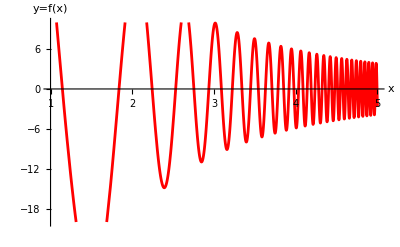

```mathematica
Plot[f[x],{x,1,5}, PlotStyle->{Red, Thickness[0.005]},
AxesLabel->{"x","y=f(x)"},AxesStyle->Arrowheads[{0.0,0.04}],
PlotRange->{-20,10}]
```

```mathematica
(*Thickness[]-grubość linii
AxesLabel->{}-podpisy osi
AxesStyle->Arrowheads[{}]-strzalki
PlotRange->{}-zakres funkcji do wyswietlenia
PlotRange->All - caly zakres
*.eps - grafika wektorowa,przydatna to TeX*)
```

```mathematica
(*zad2*)
```

```mathematica
f[x_]:=x^2+1
g[x_]:=-2*(x+1)^2+10
```

```mathematica
Solve[f[x]==g[x], x] (*przecięcia*)
```

{{x→-7/3},{x→1}}

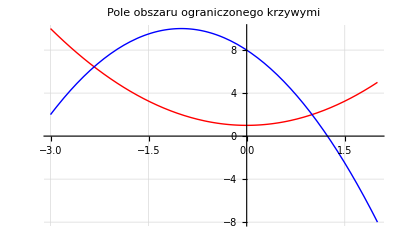

```mathematica
Plot[{f[x],g[x]},{x,-3,2},PlotStyle->{{Red, Thick},{Blue}},
PlotLabel->"Pole obszaru ograniczonego krzywymi",
GridLines->Automatic
]
```

```mathematica
(*Thick-pogrubienie
PlotLabel->""-podpis
GridLines-> - linie siatki
*)
```

```mathematica
(*Pole obszaru pomiędzy funkcjami*)
Integrate[g[x]-f[x],{x,-7/3,1}]
```

500/27

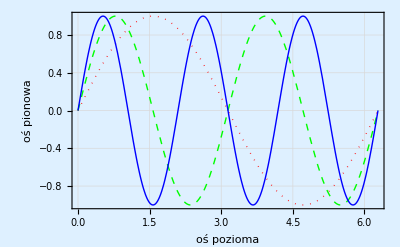

```mathematica
(*zad3*)
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},
PlotStyle->{{Red, Dotted},{Green, Dashed},{Blue}},
GridLines->Automatic,
Frame->True,
FrameLabel->{"oś pozioma","oś pionowa"},
Background->LightBlue]
```

```mathematica
(*PlotyStyle - 
Dotted - kropki
Dashed - przerywany
Frame->True - ramka
Background->kolor, albo RGBColor[x,x,x]*)
```

```mathematica
(*zad4*)
SetDirectory[NotebookDirectory[]]
```

\\Pitagoras\Profile2_Studenci\dawid.bitner\Pulpit

```mathematica
przyblizone=ReadList["dane.txt", Real]
```

{2.67651,7.60872,8.42172,9.09246,8.55902,7.6943,4.74989,5.40589,3.39101,3.33801,2.78548,2.42968,2.21147,1.53951,1.70712,1.74053,1.48388,1.07822,1.06074,1.2857,1.21935,1.23254,0.942943,0.991719,1.14471,1.05329,0.983273,1.03161,1.15366,1.25273,1.54634,1.47206,1.81742,1.69097,1.84306,2.14119,2.34049,2.1745,3.05846,3.31372,3.34854,3.02018,3.29985,3.42041,3.99355,3.98056,5.04471,5.8341,4.69652,4.79617,6.37331,6.11115,5.8344,6.88929,5.99755,6.59731,6.759,7.70372,6.41824,7.95846,8.89166,8.11946,9.29424,6.68367,9.04945,9.11858,8.91596,6.71299,8.88018,6.37765,7.46929,5.84053,6.73698,6.73719,6.66409,5.81045,5.92329,6.19482,4.89453,5.54187,4.51611,4.49462,4.01882,3.43514,3.87982,3.99525,2.95344,2.97353,3.38394,2.97404,3.21629,2.92067,2.11241,2.16802,2.63962,1.82042,1.78551,1.62752,2.1373,2.0911,1.73874}

```mathematica
przyblizone[[2]]
```

7.60872

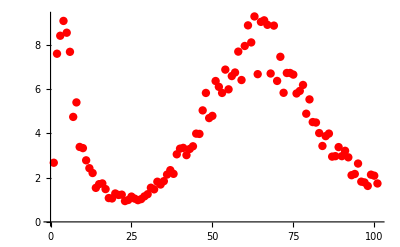

```mathematica
rys1=ListPlot[przyblizone,PlotStyle->{Red,PointSize[0.015]}]
```

```mathematica
(*SetDirectory...-działa w tym samym folderze, co plik z danymi
ReadList-czyta liste z pliku
PointSize[]-wielkość kropek*)
```

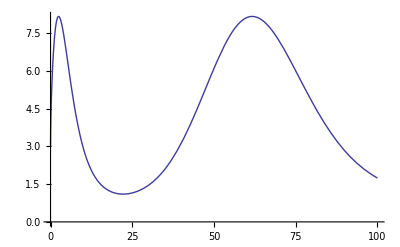

```mathematica
rys2=Plot[3*E^(Sin[Sqrt[x]]),{x,0,100}]
```

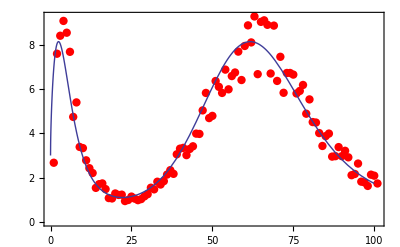

```mathematica
Show[rys1,rys2, Frame->True]
```

```mathematica
(*show pokazuje kilka wykresów na jednym*)
```

```mathematica
(*zad5*)
f[x_,y_]:=20*x*E^(-x^2-y^2)
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},
AxesLabel->{"x","y","z"},
ColorFunction->"BlueGreenYellow",
Mesh->30
]
```

-Graphics3D-

```mathematica
(*wykresem funkcji 2 zmiennych jest trójwymairowy, więc musimu użyć Plot3D
mesh odpowiada za siatkę*)
```

```mathematica
(*zad6*)
oceny={2,3,3.5,4,4.5,5};
lstudentow={5,15,20,11,7,3};
```

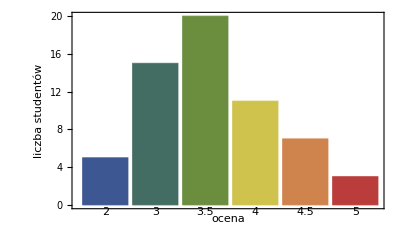

```mathematica
BarChart[lstudentow,ChartLabels->oceny, ChartStyle->"DarkRainbow", Frame->True,FrameTicks->{None, Automatic},FrameLabel->{"ocena", "liczba studentów"}]
```

```mathematica
(*BarChart - wykresy słupkowe
FrameTicks->{x,x} - czy podpisy na osiach*)
```